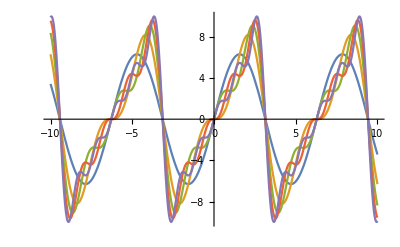

```mathematica
f[x_]:=x;
f[x_+2Pi n_]= f[x];

a[n_]=Integrate[f[x] Cos[n x],{x,-Pi,Pi}];
b[n_]=Integrate[f[x] Sin[n x],{x,-Pi,Pi}];

four[x_,k_]:=(a[0]/2 )+ Sum[  a[n] Cos[n x] + b[n] Sin[n x] ,{n,1,k}];
Plot[Evaluate[Table[four[x,j],{j,1,5}]],{x,-10,10}]
```

```mathematica
(*------------------------------------------*)
```

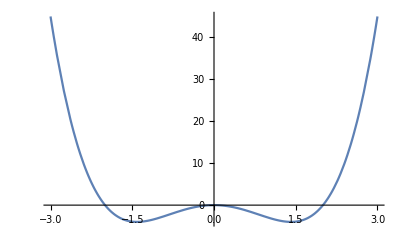

{0,-mu^2/(4 lambda),-mu^2/(4 lambda)}

-Graphics3D-

```mathematica
V[x_,mu_,lambda_]:= - mu x^2 + lambda x^4;
Plot[V[x,4,1],{x,-3,3}]
Cmaxmin=Solve[D[V[x,mu,lambda],x]==0,x];
ValmM=V[x,mu,lambda]/.Cmaxmin

ParametricPlot3D[ w=V[r,4,1]; {r Sin[phi],r Cos[phi] , w},{r,0,2},{phi,0, 2 Pi}]
```

```mathematica
(*-------------------------------------*)
```

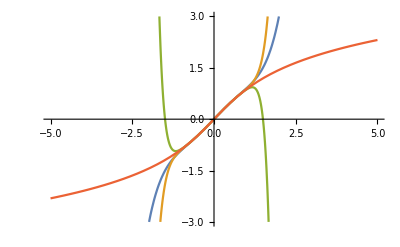

```mathematica
svil[n_]:=Normal[Series[ArcSinh[x],{x,0,n}]];

funz=Table[svil[i],{i,{5,9,11}}];

Plot[{funz,ArcSinh[x]},{x,-5,5}, PlotRange->{-3,3}]
```